```mathematica
FunctionPeriod[2*Tan[(3*π*x)/4],x]
```

4/3

```mathematica
transformFunctionByMatrix[f_,x_,y_,Smat_,Tmat_]:=Module[{xdash,plusminus},
Print["Workings:"];
Print[Smat//MatrixForm,".",{{x},{y}}//MatrixForm,"+",Tmat//MatrixForm,"=",{{x'},{y'}}//MatrixForm];
Print[(Smat.{{x},{y}}+Tmat)//MatrixForm,"=",{{x'},{y'}}//MatrixForm];
Print[{Column[{(Smat.{{x},{y}}+Tmat)[[1,1]]==x',(Smat.{{x},{y}}+Tmat)[[2,1]]==y'}]}];
plusminus=False;
If[Length[Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x]]==2,plusminus=True];
If[plusminus,
Print[{Column[{(±Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]==x)/.xdash->x',(Smat.{{x},{f}}+Tmat)[[2,1]]==y'}]}];
Print[y'==((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->HoldForm[Evaluate[±Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]/.xdash->x']])];
Print["Answer (depending on domain of f):"];
Return[{((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->(Solve[xdash==(Smat.{{x},{f}}+Tmat)[[1,1]],x][[1,1,2]]))/.xdash->x',((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->(-Solve[xdash==(Smat.{{x},{f}}+Tmat)[[1,1]],x][[1,1,2]]))/.xdash->x'}];
,
Print[{Column[{(Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]==x)/.xdash->x',(Smat.{{x},{f}}+Tmat)[[2,1]]==y'}]}];
Print[y'==((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->HoldForm[Evaluate[Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]/.xdash->x']])];
Print["Answer:"];
Return[((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->(Solve[xdash==(Smat.{{x},{f}}+Tmat)[[1,1]],x][[1,1,2]]))/.xdash->x'];
];
];
```

```mathematica
transformFunctionByMatrix[x^2,x,y,matrix2x2[0,a,b,0],matrix1x2[c,d]]
```

Workings:

(0 | a
b | 0).(x
y)+(c
d)=(x'
y')

(c+a y
d+b x)=(x'
y')

{c+a y==x'
d+b x==y'}

{±(-(√(-c+x'))/(√a))==x
d+b x==y'}

y'==d+b (±(-(√(-c+x'))/(√a)))

Answer (depending on domain of f):

{d-(b √(-c+x'))/(√a),d+(b √(-c+x'))/(√a)}

```mathematica
transformFunctionByMatrix[x^2,x,y,matrix2x2[a,0,0,b],matrix1x2[c,d]]
```

Workings:

(a | 0
0 | b).(x
y)+(c
d)=(x'
y')

(c+a x
d+b y)=(x'
y')

{c+a x==x'
d+b y==y'}

{(-c+x')/a==x
d+b x^2==y'}

y'==d+b ((-c+x')/a)^2

Answer:

d+(b (-c+x')^2)/a^2

```mathematica
rangeOfFunction[f_,x_,sdom_:True]:=Module[{i,skippedIfStatment,keyPoints,endPoints,yEndPoints,vAsy,min,max,op1,op2,bracket1,bracket2},
keyPoints=turningPoints[f,x,sdom][[All,1]];
skippedIfStatment=True;
endPoints={};
If[sdom,skippedIfStatment=False];
If[skippedIfStatment,
If[Length[sdom]==2,
AppendTo[endPoints,valueOfInequality[sdom,x]];
,
AppendTo[endPoints,sdom[[1]]];
AppendTo[endPoints,sdom[[3]]];
If[sdom[[0]]==Inequality,
endPoints={};
AppendTo[endPoints,sdom[[1]]];
AppendTo[endPoints,sdom[[5]]];
];
];
];
yEndPoints=f/.x->endPoints;
keyPoints=f/.x->keyPoints;
If[skippedIfStatment,
If[Or[
And[Length[sdom]==2,sdom[[1]]==x,Or[sdom[[0]]==Less,sdom[[0]]==LessEqual]],
And[Length[sdom]==2,sdom[[2]]==x,Or[sdom[[0]]==Greater,sdom[[0]]==GreaterEqual]],
],
AppendTo[keyPoints,Limit[f,x->-∞]];
];
If[Or[
And[Length[sdom]==2,sdom[[1]]==x,Or[sdom[[0]]==Greater,sdom[[0]]==GreaterEqual]],
And[Length[sdom]==2,sdom[[2]]==x,Or[sdom[[0]]==Less,sdom[[0]]==LessEqual]],
],
AppendTo[keyPoints,Limit[f,x->∞]];
];
,
AppendTo[keyPoints,Limit[f,x->-∞]];
AppendTo[keyPoints,Limit[f,x->∞]];
];
vAsy=verticleAsymptotes[f,x];
For[i=1,i≤Length[vAsy],i++,
If[Not[FullSimplify[x==vAsy[[i]]&&sdom]],
Continue[];
];
AppendTo[keyPoints,Limit[f,x->vAsy[[i]],Direction->"FromAbove"]];
AppendTo[keyPoints,Limit[f,x->vAsy[[i]],Direction->"FromBelow"]];
];
keyPoints=DeleteDuplicates[keyPoints];
min=Min[Join[keyPoints,yEndPoints]];
max=Max[Join[keyPoints,yEndPoints]];
op1:=LessEqual;
op2:=LessEqual;
If[min==-∞,op1:=Less];
If[max==∞,op2:=Less];

If[And[Length[sdom]==5,sdom[[0]]==Inequality,min==f/.x->sdom[[1]]],
op1:=sdom[[2]];
];
If[And[Length[sdom]==5,sdom[[0]]==Inequality,min==f/.x->sdom[[5]]],
op1:=sdom[[4]];
];
If[And[Length[sdom]==5,sdom[[0]]==Inequality,max==f/.x->sdom[[1]]],
op2:=sdom[[2]];
];
If[And[Length[sdom]==5,sdom[[0]]==Inequality,max==f/.x->sdom[[5]]],
op2:=sdom[[4]];
];
If[And[Length[sdom]==3,min==f/.x->sdom[[1]]],
op1:=sdom[[0]];
];
If[And[Length[sdom]==3,min==f/.x->sdom[[3]]],
op1:=sdom[[0]];
];
If[And[Length[sdom]==3,max==f/.x->sdom[[1]]],
op2:=sdom[[0]];
];
If[And[Length[sdom]==3,max==f/.x->sdom[[3]]],
op2:=sdom[[0]];
];
If[And[Length[sdom]==2,sdom[[1]]==x,min==f/.x->sdom[[2]]],
If[sdom[[0]]==Less,op1:=Less];
If[sdom[[0]]==Greater,op1:=Less];
];
If[And[Length[sdom]==2,sdom[[2]]==x,min==f/.x->sdom[[1]]],
If[sdom[[0]]==Less,op1:=Less];
If[sdom[[0]]==Greater,op1:=Less];
];
If[And[Length[sdom]==2,sdom[[1]]==x,max==f/.x->sdom[[2]]],
If[sdom[[0]]==Less,op2:=Less];
If[sdom[[0]]==Greater,op2:=Less];
];
If[And[Length[sdom]==2,sdom[[2]]==x,max==f/.x->sdom[[1]]],
If[sdom[[0]]==Less,op2:=Less];
If[sdom[[0]]==Greater,op2:=Less];
];

bracket1="[";
If[op1==Less,
bracket1="(";
];
bracket2="]";
If[op2==Less,
bracket2=")";
];
Print[bracket1,min,",",max,bracket2];
Return[FullSimplify[op1[min,x]&&op2[x,max]]];
];
```

```mathematica
rangeOfFunction[x^2,x,1<=x]
```

[1,∞)

x≥1

```mathematica
averageRateOfChange[f_,x_,a_,b_]:=1/(b-a)*((f/.x->b)-(f/.x->a))
nAverageRateOfChange[f_,x_,a_,b_]:=N[1/(b-a)*((f/.x->b)-(f/.x->a))]
```

```mathematica
matrix2x2[a_,b_,c_,d_]:={{a,b},{c,d}}
matrix1x2[a_,b_]:={{a},{b}}
```

```mathematica
matrix2x2[a,b,c,d]
```

{{a,b},{c,d}}

```mathematica
matrix1x2[a,b]
```

{{a},{b}}

```mathematica
{{1,0},{0,1}}//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
nonSignedIntegral[f_,x_]:=Abs[Integrate[f,x]]
semiEvaluateIntegral[f_,x_,a_,b_,c_:0]:=Abs[Integrate[f,{x,a,b}]]==c//HoldForm
boundedArea[f_,x_]:=
Module[{var,roots,total},
var=x[[1]];
roots=Reduce[f<0&&x[[2]]≤var≤x[[3]],var];
total=0;
If[roots[[0]]==Or,
If[x[[2]]≠roots[[1,1]],
total=total+nonSignedIntegral[f,{var,x[[2]],roots[[1,1]]}];
Print[semiEvaluateIntegral[f,var,x[[2]],roots[[1,1]],nonSignedIntegral[f,{var,x[[2]],roots[[1,1]]}]]];
];
For[i=1,i≤Length[roots],i++,
If[i>1,
total=total+nonSignedIntegral[f,{var,roots[[i-1,5]],roots[[i,1]]}];
Print[semiEvaluateIntegral[f,var,roots[[i-1,5]],roots[[i,1]],nonSignedIntegral[f,{var,roots[[i-1,5]],roots[[i,1]]}]]];
];
total=total+nonSignedIntegral[f,{var,roots[[i,1]],roots[[i,5]]}];
Print[semiEvaluateIntegral[f,var,roots[[i,1]],roots[[i,5]],nonSignedIntegral[f,{var,roots[[i,1]],roots[[i,5]]}]]];
];
If[roots[[i-1,5]]≠x[[3]],
total=total+nonSignedIntegral[f,{var,roots[[i-1,5]],x[[3]]}];
Print[semiEvaluateIntegral[f,var,roots[[i-1,5]],x[[3]],nonSignedIntegral[f,{var,roots[[i-1,5]],x[[3]]}]]];
];
];
If[roots[[0]]==Inequality,
If[x[[2]]≠roots[[1]],
total=total+nonSignedIntegral[f,{var,x[[2]],roots[[1]]}];
Print[semiEvaluateIntegral[f,var,x[[2]],roots[[1]],nonSignedIntegral[f,{var,x[[2]],roots[[1]]}]]];
];
total=total+nonSignedIntegral[f,{var,roots[[1]],roots[[5]]}];
Print[semiEvaluateIntegral[f,var,roots[[1]],roots[[5]],nonSignedIntegral[f,{var,roots[[1]],roots[[5]]}]]];
If[roots[[5]]≠x[[3]],
total=total+nonSignedIntegral[f,{var,roots[[5]],x[[3]]}];
Print[semiEvaluateIntegral[f,var,roots[[5]],x[[3]],nonSignedIntegral[f,{var,roots[[5]],x[[3]]}]]];
];
];
Return[total];
]
```

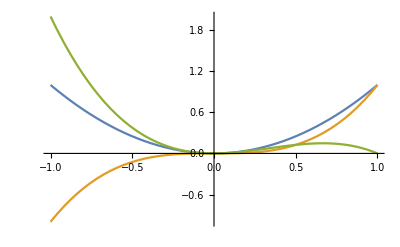

```mathematica
Plot[{x^2,x^3,x^2-x^3},{x,-1,1}]
```

```mathematica
Max[roots[x^2-x^3,x]]
```

1

```mathematica
enclosedArea[f1_,f2_,x_]:=Module[{i,var,intersections,min,max},
var=x[[1]];
intersections=DeleteDuplicates[roots[f2-f1,var]];
min=intersections[[1,1]];
max=intersections[[1,1]];
For[i=1,i≤Length[intersections],i++,
If[intersections[[i,1]]<min,min=intersections[[i,1]]];
If[intersections[[i,1]]>max,max=intersections[[i,1]]];
];
If[x[[2]]>min,min=x[[2]]];
If[x[[3]]<max,max=x[[3]]];
Return[boundedArea[f2-f1,{var,min,max}]];
];
```

```mathematica
enclosedArea[x^2,x^3,{x,0,2}]
```

Abs[∫_0^1 (-x^2+x^3)ⅆx]==1/12

1/12

```mathematica
roots[f_,x_,sdom_:True]:=Module[{i,rawSol,root,output},
rawSol=Solve[f==0&&sdom,x,Reals];
root={};
output={};
For[i=1,i≤Length[rawSol],i++,
If[rawSol[[i,1,2,0]]==Root,
AppendTo[root,N[rawSol[[i]],2]];
Continue[];
];
AppendTo[root,rawSol[[i]]];
];
If[Or[root=={{}},root=={}],
Return[{}],
For[i=1,i≤Length[root],i++,
AppendTo[output, {root[[i,1,2]],0}];
];
Return[output]
];
];
approximateRoots[solutions_]:=Module[{i, output},
output={};
For[i=1,i≤Length[solutions],i++,
If[solutions[[i,1,2,0]]==Root,
AppendTo[output, N[solutions[[i]],2]];
Continue[];
];
AppendTo[output, solutions[[i]]];
];
Return[output];
];
```

```mathematica
convertNormalDistributionValues[mean1_,stdev1_,val_,mean2_,stdev2_]:=mean2+(((val-mean1)/stdev1)*stdev2)
```

```mathematica
convertNormalDistributionValues[100,15,130,0,1]
```

2